## Zooniverse Data

```mathematica
rawData=Import["/Users/katjad/Documents/CitizenScienceData/CitizenScienceData/data_zooniverse_weeklyclasscount.csv"]//Rest
```

{{2019,1,641728,2018-12-31T00:00:00.000Z},{2019,2,949901,2019-01-07T00:00:00.000Z},{2019,3,1198068,2019-01-14T00:00:00.000Z},{2019,4,1320653,2019-01-21T00:00:00.000Z},{2019,5,1314642,2019-01-28T00:00:00.000Z},{2019,6,1379959,2019-02-04T00:00:00.000Z},{2019,7,1345116,2019-02-11T00:00:00.000Z},{2019,8,1341442,2019-02-18T00:00:00.000Z},{2019,9,1771089,2019-02-25T00:00:00.000Z},{2019,10,1725370,2019-03-04T00:00:00.000Z},{2019,11,1834962,2019-03-11T00:00:00.000Z},{2019,12,1752865,2019-03-18T00:00:00.000Z},{2019,13,1682296,2019-03-25T00:00:00.000Z},{2019,14,1692163,2019-04-01T00:00:00.000Z},{2019,15,1596167,2019-04-08T00:00:00.000Z},{2019,16,836119,2019-04-15T00:00:00.000Z},{2019,17,1204340,2019-04-22T00:00:00.000Z},{2019,18,1362895,2019-04-29T00:00:00.000Z},{2019,19,1146540,2019-05-06T00:00:00.000Z},{2019,20,1571366,2019-05-13T00:00:00.000Z},{2019,21,1166699,2019-05-20T00:00:00.000Z},{2019,22,1160943,2019-05-27T00:00:00.000Z},{2019,23,735014,2019-06-03T00:00:00.000Z},{2019,24,647291,2019-06-10T00:00:00.000Z},{2019,25,1175384,2019-06-17T00:00:00.000Z},{2019,26,1107249,2019-06-24T00:00:00.000Z},{2019,27,821761,2019-07-01T00:00:00.000Z},{2019,28,946309,2019-07-08T00:00:00.000Z},{2019,29,1210007,2019-07-15T00:00:00.000Z},{2019,30,1068332,2019-07-22T00:00:00.000Z},{2019,31,1085387,2019-07-29T00:00:00.000Z},{2019,32,882788,2019-08-05T00:00:00.000Z},{2019,33,792397,2019-08-12T00:00:00.000Z},{2019,34,968225,2019-08-19T00:00:00.000Z},{2019,35,847177,2019-08-26T00:00:00.000Z},{2019,36,893725,2019-09-02T00:00:00.000Z},{2019,37,1154154,2019-09-09T00:00:00.000Z},{2019,38,744877,2019-09-16T00:00:00.000Z},{2019,39,841687,2019-09-23T00:00:00.000Z},{2019,40,805271,2019-09-30T00:00:00.000Z},{2019,41,747915,2019-10-07T00:00:00.000Z},{2019,42,748520,2019-10-14T00:00:00.000Z},{2019,43,1036027,2019-10-21T00:00:00.000Z},{2019,44,1131038,2019-10-28T00:00:00.000Z},{2019,45,1126243,2019-11-04T00:00:00.000Z},{2019,46,969232,2019-11-11T00:00:00.000Z},{2019,47,918404,2019-11-18T00:00:00.000Z},{2019,48,808690,2019-11-25T00:00:00.000Z},{2019,49,1120584,2019-12-02T00:00:00.000Z},{2019,50,1087621,2019-12-09T00:00:00.000Z},{2019,51,967275,2019-12-16T00:00:00.000Z},{2019,52,980088,2019-12-23T00:00:00.000Z},{2020,1,922262,2019-12-30T00:00:00.000Z},{2020,2,1061324,2020-01-06T00:00:00.000Z},{2020,3,1220054,2020-01-13T00:00:00.000Z},{2020,4,868795,2020-01-20T00:00:00.000Z},{2020,5,1015904,2020-01-27T00:00:00.000Z},{2020,6,1092604,2020-02-03T00:00:00.000Z},{2020,7,909930,2020-02-10T00:00:00.000Z},{2020,8,891532,2020-02-17T00:00:00.000Z},{2020,9,1034009,2020-02-24T00:00:00.000Z},{2020,10,1498343,2020-03-02T00:00:00.000Z},{2020,11,1416407,2020-03-09T00:00:00.000Z},{2020,12,1918096,2020-03-16T00:00:00.000Z},{2020,13,3978436,2020-03-23T00:00:00.000Z},{2020,14,4693537,2020-03-30T00:00:00.000Z},{2020,15,3851184,2020-04-06T00:00:00.000Z},{2020,16,3162819,2020-04-13T00:00:00.000Z},{2020,17,3478260,2020-04-20T00:00:00.000Z},{2020,18,4225844,2020-04-27T00:00:00.000Z},{2020,19,2855639,2020-05-04T00:00:00.000Z},{2020,20,3345164,2020-05-11T00:00:00.000Z},{2020,21,3626490,2020-05-18T00:00:00.000Z},{2020,22,2939531,2020-05-25T00:00:00.000Z},{2020,23,2273240,2020-06-01T00:00:00.000Z},{2020,24,2193305,2020-06-08T00:00:00.000Z}}

```mathematica
{"year","week","count","date"}
```

```mathematica
zooniverseData=MapAt[#[[2;;3]]&,GroupBy[rawData,#[[1]]&],{All,All}];
```

```mathematica
ResourceFunction["ColorBrewerData"]["RdBu",2]
```

FunctionRepository`$cb2edf2c655749de9e1c90cb79dff58a`ColorBrewerData::subsamplecolorscheme: Color scheme RdBu has as least 3 colors, subsampling will be used to get 2 color(s).

{RGBColor[Rational[239, 255], Rational[46, 85], Rational[98, 255]],RGBColor[Rational[103, 255], Rational[169, 255], Rational[69, 85]]}

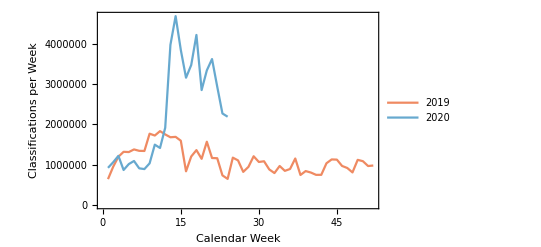

```mathematica
ListLinePlot[Values[zooniverseData],PlotRange->All,Frame->True,FrameLabel->{"Calendar Week","Classifications per Week"},PlotLegends->{"2019","2020"},PlotTheme->{"LargeLabels"},PlotStyle->ResourceFunction["ColorBrewerData"]["RdBu",2]]
```